```mathematica
Clear[a,μ, dr, eps,Q, kb, T]
μ=1*10^-2;
osseen[r_]:=1/(8 π μ)(IdentityMatrix[Length[r]]/Norm[r]+Outer[Times,r, r]/Norm[r]^3);
kernel[r_,a_]:=1/(((a/1.256)^2 π)^(3/2))Exp[(-r.r)/(a/1.256)^2];
nd[r_]:=(1/Norm[r])^3;

debye[r_]:=((eps kb T)/(2 nd[r] Q^2))^(1/2);

RPYl[r_,a_]:=1/(6 π μ a)(((3a)/(4 Norm[r])+a^3/(2 Norm[r]^3))IdentityMatrix[Length[r]]+((3a)/(4 Norm[r])-(3 a^3)/(2 Norm[r]^3))Outer[Times,r, r]/Norm[r]^2);
RPYs[r_,a_]:=1/(6 π μ a)((1-(9 Norm[r])/(32 a))IdentityMatrix[Length[r]]+((3 Norm[r])/(32 a))Outer[Times,r, r]/Norm[r]^2);
RPY[r_,a_]:=Which[Norm[r]≤2a,RPYs[r,a],Norm[r]> 2a,RPYl[r,a]];

dryTensor[r_,a_]:=1/(6 π μ a)IdentityMatrix[Length[r]];
coulomb[r_]:=Q^2/(4 π eps)r/Norm[r]^3;

coulombScreened[r_]:=Q^2/(4 π eps)(Exp[-Norm[r]/debye[r]](r+debye[r])r)/(Norm[r]^3 debye[r]);

p4[r_]:=Which[Abs[r]/dr≤1,(3-2 Abs[r]/dr+(1+4 Abs[r]/dr-4 r^2/dr^2)^(1/2))/8,
1<Abs[r]/dr≤2,(5-2 Abs[r]/dr-(-7+12 Abs[r]/dr-4 r^2/dr^2)^(1/2))/8,
 Abs[r]/dr ≥ 2,0];

p3[r_]:=Which[Abs[r]/dr≤0.5,(1+(1-3 r^2/dr^2)^(1/2))/3,
0.5<Abs[r]/dr≤1.5,(5-3 Abs[r]/dr-(-3(1- Abs[r]/dr)^2+1)^(1/2))/6,
 Abs[r]/dr ≥ 1.5,0];

peskin4[r_]:=p4[r[[1]]]p4[r[[2]]]p4[r[[3]]]/dr^3;
peskin3[r_]:=p3[r[[1]]]p3[r[[2]]]p3[r[[3]]]/dr^3;
```

2

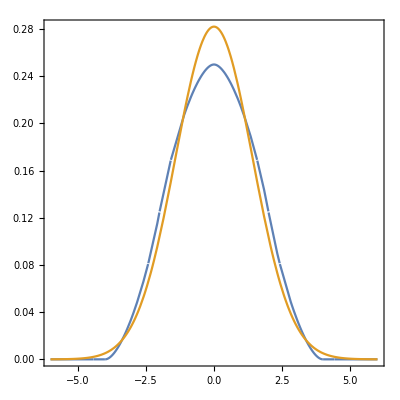

```mathematica
dr=2
Plot[{p4[r]/dr,1/(dr π^(1/2))Exp[-r^2/dr^2]},{r,-3 dr,3dr},Axes->False,Frame->True,AspectRatio->1]
```

```mathematica
Integrate[1/(dr π^(1/2))Exp[-r^2/dr^2],{r,-∞,∞}]
Integrate[p4[r]/dr,{r,-∞,∞}]
```

1

1

```mathematica
T=295;
kb=1.38065*10^-16;
diff=0.5(1.17+1.33)*10^-5;
diffA=(1.17)*10^-5;
diffB=(1.33)*10^-5;
μ=0.01;
Q=1.6*10^-19;
eps = 692.96*10^-21;
aReal=(kb T)/(diff μ 6 π)
aA=(kb T)/(diffA μ 6 π)
aB=(kb T)/(diffB μ 6 π)

(aA+aB)/2
```

1.7286×10^-8

1.84679×10^-8

1.62462×10^-8

1.73571×10^-8

```mathematica
n=4*5*2*6.02*10^19
radsA=(1/n^(1/3))/aReal
radsB=0.55*(1/n^(1/3))/aReal
radsR=4.326863*10^-8/aReal
```

2.408×10^21

4.31605

2.37383

2.5031

```mathematica
velRPY[r_,a_,sep_]:= RPY[r,a].(coulomb[sep]);
velDry[r_,a_,sep_]:= dryTensor[r,a].coulomb[sep];

velRPYscreened[r_,a_,sep_]:= RPY[r,a].(coulombScreened[sep]);
velDryscreened[r_,a_,sep_]:= dryTensor[r,a].coulombScreened[sep];
```

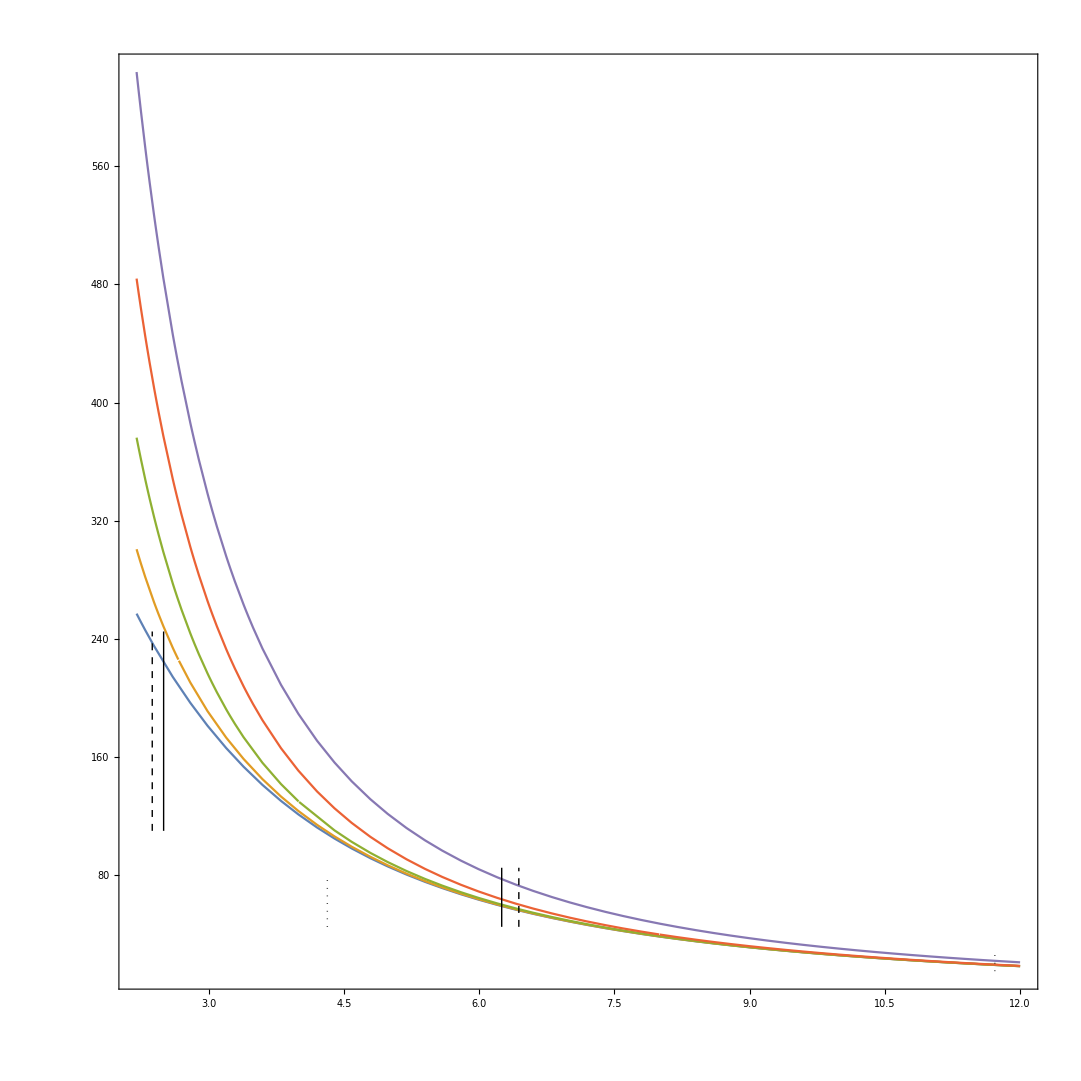

```mathematica
pa=Plot[{
velRPY[aReal{r,0,0},aReal,-aReal{r,0,0}][[1]]+velDry[aReal{0,0,0},aReal,aReal{r,0,0}][[1]],
velRPY[aReal{r,0,0},1.3333aReal,-aReal{r,0,0}][[1]]+velDry[aReal{0,0,0},aReal,aReal{r,0,0}][[1]],
velRPY[aReal{r,0,0},2aReal,-aReal{r,0,0}][[1]]+velDry[aReal{0,0,0},aReal,aReal{r,0,0}][[1]],
velRPY[aReal{r,0,0},4aReal,-aReal{r,0,0}][[1]]+velDry[aReal{0,0,0},aReal,aReal{r,0,0}][[1]],
velDry[aReal{0,0,0},aReal,aReal{r,0,0}][[1]]}
,{r,2.2,12},PlotRange->All];
pb1=Graphics[{Line[{{6.25,45},{6.25,85}}],Dashed,Line[{{6.44,45},{6.44,85}}],Dotted,Line[{{11.72,15},{11.72,28}}]}];
pb2=Graphics[{Line[{{3.70,110},{3.70,245}}],Dashed,Line[{{3.77,110},{3.77,245}}],Dotted,Line[{{6.85,45},{6.85,80}}]}];
pb3=Graphics[{Line[{{2.5,110},{2.5,245}}],Dashed,Line[{{2.3738,110},{2.3738,245}}],Dotted,Line[{{4.3160,45},{4.3160,80}}]}];
Show[pa,pb1,pb3,Frame->True,AspectRatio->1,Axes->False]
```

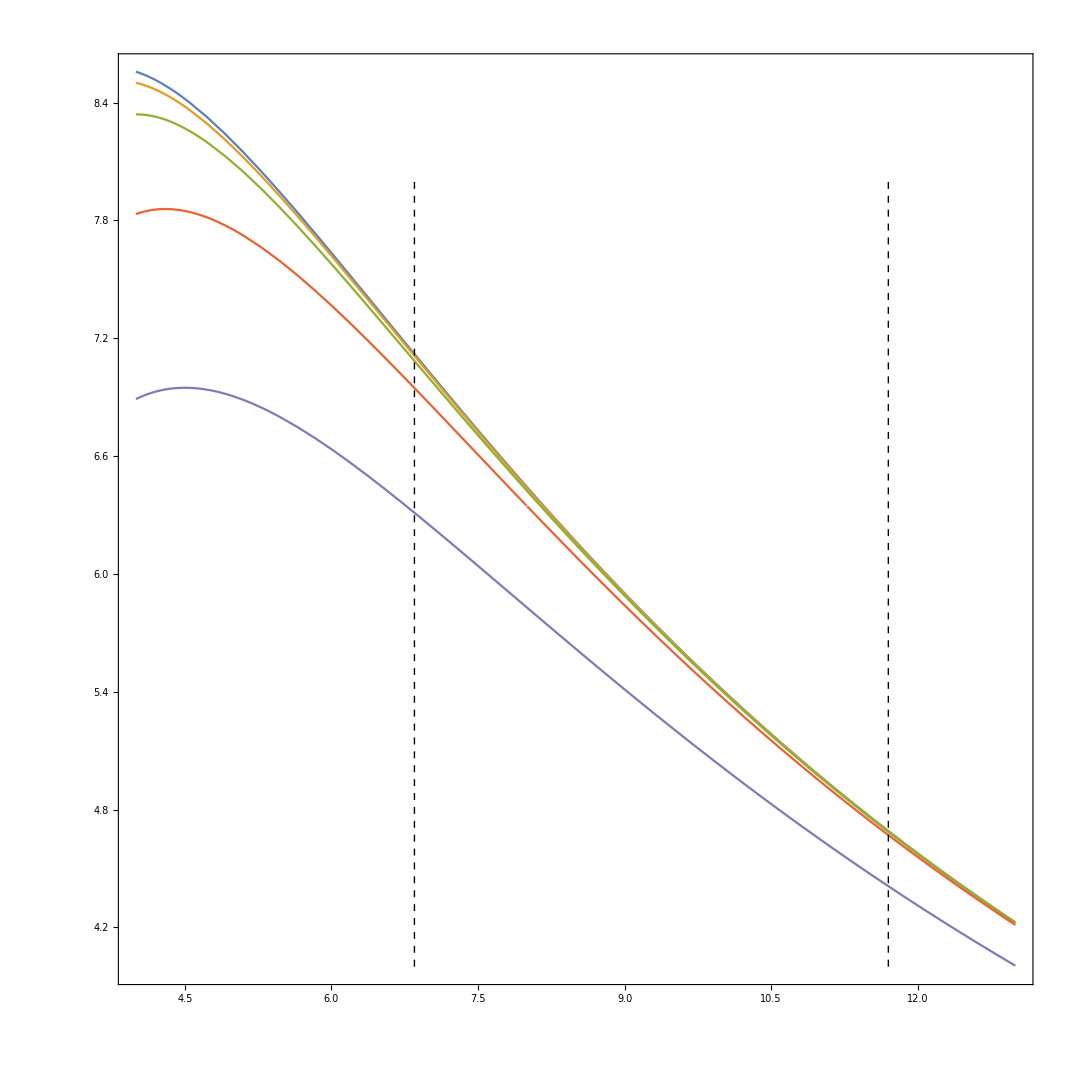

6.41282

7.28979

6.85131

6.85131

```mathematica
pa=Plot[{
velRPYscreened[aReal{r,0,0},aReal,-aReal{r,0,0}][[1]]+velDryscreened[aReal{0,0,0},aReal,aReal{r,0,0}][[1]],
velRPYscreened[aReal{r,0,0},1.3333aReal,-aReal{r,0,0}][[1]]+velDryscreened[aReal{0,0,0},aReal,aReal{r,0,0}][[1]],
velRPYscreened[aReal{r,0,0},2aReal,-aReal{r,0,0}][[1]]+velDryscreened[aReal{0,0,0},aReal,aReal{r,0,0}][[1]],
velRPYscreened[aReal{r,0,0},4aReal,-aReal{r,0,0}][[1]]+velDryscreened[aReal{0,0,0},aReal,aReal{r,0,0}][[1]],
velDryscreened[aReal{0,0,0},aReal,aReal{r,0,0}][[1]]}
,{r,4,13},PlotRange->All];
pb=Graphics[{Dashed,Line[{{6.85,4},{6.85,8}}],Line[{{11.7,4},{11.7,8}}]}];
Show[pa,pb,Frame->True,AspectRatio->1,Axes->False]
```

2.02515×10^-7

1.11383×10^-7

1.08×10^-7

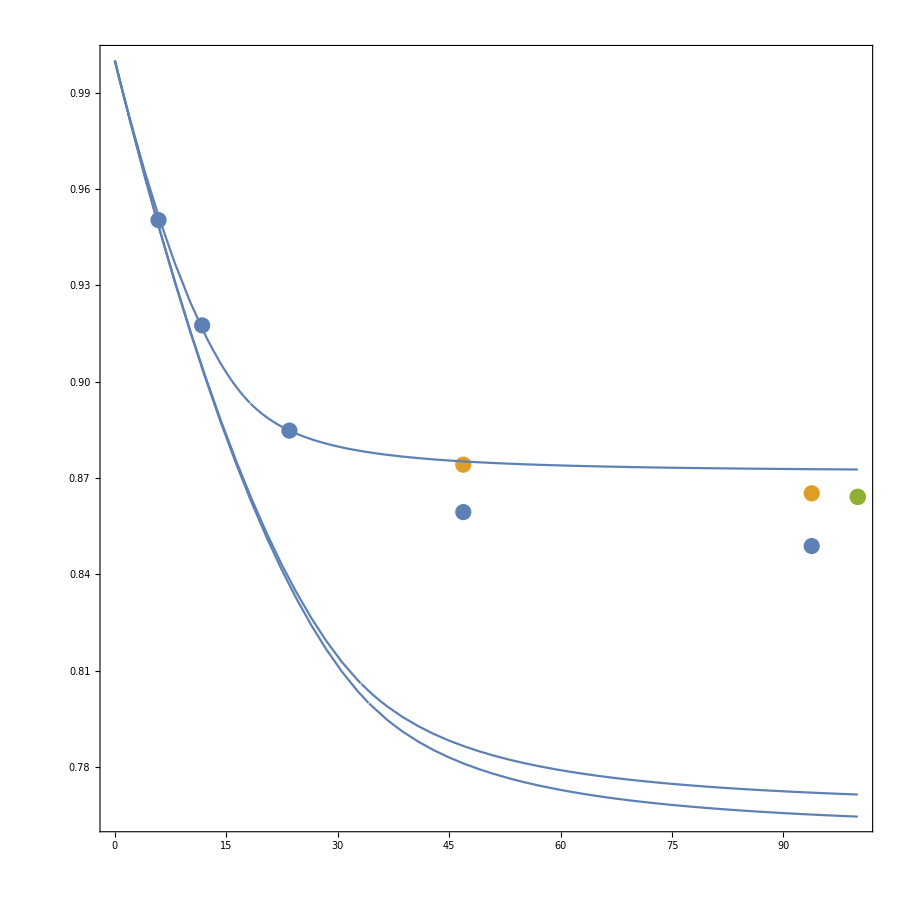

0.848837

6.85131

```mathematica
n=2*6.02*10^19;
radsA=(1/n^(1/3))
radsB=0.55*radsA
radsR=1.08*10^-7

rads=0.55radsM;
pointsZero={{93.8,8.03/9.46},{46.9,8.13/9.46},{23.5,8.37/9.46},{11.75,8.68/9.46},{5.88,8.99/9.46}};
pointsWeak={{93.8,7.77/8.98},{46.9,7.85/8.98}};
pointsTheory={{100,7.76/8.98}};
pointsStrong={{93.8,8.37/9.43},{46.9,8.41/9.43}};
pc=ListPlot[{pointsZero,pointsWeak,pointsTheory}];
pd=Plot[{
(velRPY[{radsA,0,0},(kb T)/(0.5(per/100 diffA+0.881 per/100 diffB) 6 μ π),-{radsA,0,0}][[1]]+velDry[{0,0,0},aReal,{radsA,0,0}][[1]])/(velDry[{0,0,0},aReal,{radsA,0,0}][[1]])
},{per,0,100},PlotRange->All];
pe=Plot[{
(velRPY[{radsB,0,0},(kb T)/(0.5(per/100 diffA+0.881 per/100 diffB) 6 μ π),-{radsB,0,0}][[1]]+velDry[{0,0,0},aReal,{radsB,0,0}][[1]])/(velDry[{0,0,0},aReal,{radsB,0,0}][[1]])
},{per,0,100},PlotRange->All];
pf=Plot[{
(velRPY[{radsR,0,0},(kb T)/(0.5(per/100 diffA+0.881 per/100 diffB) 6 μ π),-{radsR,0,0}][[1]]+velDry[{0,0,0},aReal,{radsR,0,0}][[1]])/(velDry[{0,0,0},aReal,{radsR,0,0}][[1]])
},{per,0,100},PlotRange->All];
Show[pc,pd,pe,pf,PlotRange->All,Frame->True,AspectRatio->1,Axes->False]
```

1.18432×10^-7

6.51374×10^-8

6.39×10^-8

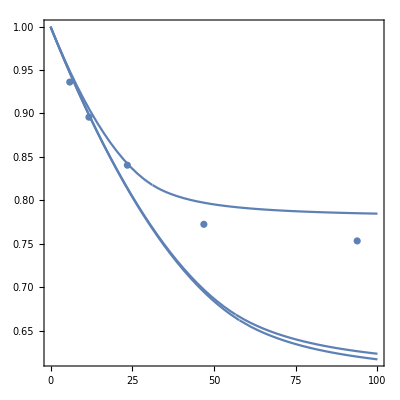

```mathematica
n=5*2*6.02*10^19;
radsA=(1/n^(1/3))
radsB=0.55*radsA
radsR=6.39*10^-8

pointsZero={{5.88,4.4/4.7},{11.75,4.21/4.70},{23.5,3.95/4.70},{46.9,3.63/4.70},{93.8,3.54/4.70}};
pc=ListPlot[{pointsZero}];
pd=Plot[{
(velRPY[{radsA,0,0},(kb T)/(per/100 diffA 6 μ π),-{radsA,0,0}][[1]]+velDry[{0,0,0},aReal,{radsA,0,0}][[1]])/(velDry[aReal{0,0,0},aReal,{radsA,0,0}][[1]])
},{per,0,100},PlotRange->All];
pe=Plot[{
(velRPY[{radsB,0,0},(kb T)/(0.5(per/100 diffA+0.881 per/100 diffB) 6 μ π),-{radsB,0,0}][[1]]+velDry[{0,0,0},aReal,{radsB,0,0}][[1]])/(velDry[{0,0,0},aReal,{radsB,0,0}][[1]])
},{per,0,100},PlotRange->All];
pf=Plot[{
(velRPY[{radsR,0,0},(kb T)/(0.5(per/100 diffA+0.881 per/100 diffB) 6 μ π),-{radsR,0,0}][[1]]+velDry[{0,0,0},aReal,{radsR,0,0}][[1]])/(velDry[{0,0,0},aReal,{radsR,0,0}][[1]])
},{per,0,100},PlotRange->All];
Show[pc,pd,pe,pf,Frame->True,PlotRange->All,AspectRatio->1,Axes->False]
```

7.46073×10^-8

4.1034×10^-8

4.32686×10^-8

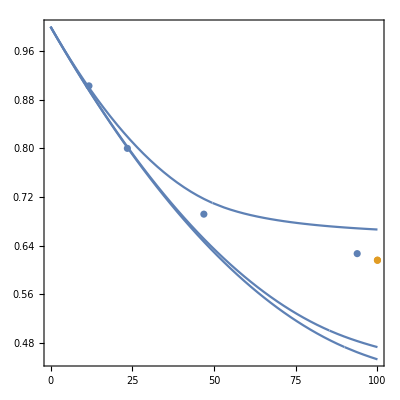

```mathematica
n=20*2*6.02*10^19;
radsA=(1/n^(1/3))
radsB=0.55*radsA
radsR=4.326863*10^-8

pointsZero={{11.75,1.67/1.85},{23.5,1.48/1.85},{46.9,1.28/1.85},{93.8,1.16/1.85}};
pointsTheory={{100,1.14/1.85}};
pc=ListPlot[{pointsZero,pointsTheory}];
pd=Plot[{
(velRPY[{radsA,0,0},(kb T)/(per/100 diffA 6 μ π),-{radsA,0,0}][[1]]+velDry[{0,0,0},aReal,{radsA,0,0}][[1]])/(velDry[aReal{0,0,0},aReal,{radsA,0,0}][[1]])
},{per,0,100},PlotRange->All];
pe=Plot[{
(velRPY[{radsB,0,0},(kb T)/(0.5(per/100 diffA+0.881 per/100 diffB) 6 μ π),-{radsB,0,0}][[1]]+velDry[{0,0,0},aReal,{radsB,0,0}][[1]])/(velDry[{0,0,0},aReal,{radsB,0,0}][[1]])
},{per,0,100},PlotRange->All];
pf=Plot[{
(velRPY[{radsR,0,0},(kb T)/(0.5(per/100 diffA+0.881 per/100 diffB) 6 μ π),-{radsR,0,0}][[1]]+velDry[{0,0,0},aReal,{radsR,0,0}][[1]])/(velDry[{0,0,0},aReal,{radsR,0,0}][[1]])
},{per,0,100},PlotRange->All];
Show[pc,pd,pe,pf,Frame->True,PlotRange->All,AspectRatio->1,Axes->False]
```

```mathematica
Q/(kb T)10^14 0.96*10^-7
```

37.7125

```mathematica
Q 10^14
```

0.000016

```mathematica
velRPY[aReal{10,0,0},aReal,-aReal{10,0,0}][[1]]
velRPY[aReal{0.000001,0,0},aReal,aReal{10,0,0}][[1]]
velField[aReal{0.000001,0,0},aReal,aReal{10,0,0}][[1]]
```

-3.68936

24.7608

4596.21

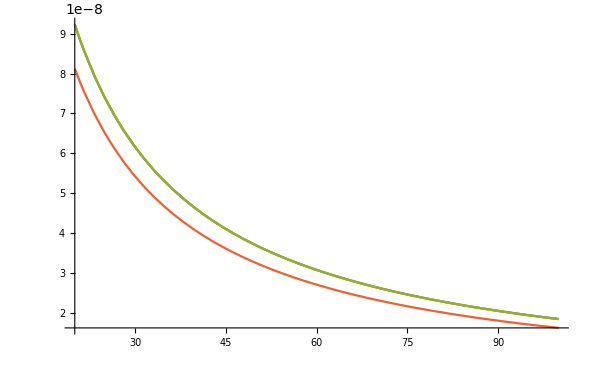

```mathematica
Plot[{(kb T)/(0.5(per/100 diffA+0.881 per/100 diffB) 6 μ π),0.5((kb T)/((per/100 diffA) 6 μ π)+(kb T)/((0.881 per/100 diffB) 6 μ π)),((kb T)/((per/100 diffA) 6 μ π)),((kb T)/((per/100 diffB) 6 μ π))},{per,20,100}]
```

```mathematica
n=5*6.02*10^19;
(1/n^(1/3))
0.55(1/n^(1/3))
```

1.49215×10^-7

8.2068×10^-8

```mathematica
dataA=Import["/home/drladiges/kumonga/projects/FHDeX/exec/NN_test4/nearestNeighbour","Table"];
```

```mathematica
Mean[dataA[[-3;;-1]]]
```

{5.89375×10^-8,4.57637×10^-8,4.57889×10^-8,5.92056×10^-8,4.32686×10^-8}

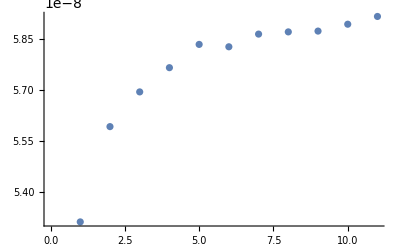

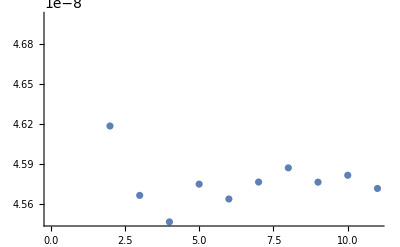

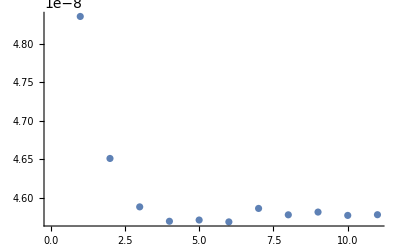

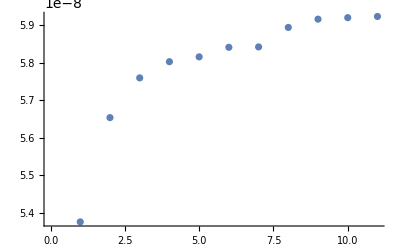

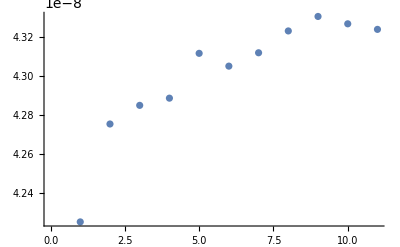

```mathematica
ListPlot[dataA[[All,1]]]
ListPlot[dataA[[All,2]]]
ListPlot[dataA[[All,3]]]
ListPlot[dataA[[All,4]]]
ListPlot[dataA[[All,5]]]
```

```mathematica
n=20*2*6.02*10^19;
radsA=(1/n^(1/3))/aReal
radsB=0.55*(1/n^(1/3))/aReal
```

4.31605

2.37383

{{{93.8,1/100},ErrorBar[3/500]},{{46.9,1/500},ErrorBar[7/1000]},{{23.5,1/50},ErrorBar[7/1000]},{{11.75,13/1000},ErrorBar[1/500]},{{5.88,19/500},ErrorBar[1/125]},{{0,43/500},ErrorBar[3/500]}}

{{{93.8,0.0347938},ErrorBar[0.00515464]},{{46.9,0.0476804},ErrorBar[0.00386598]},{{23.5,0.0786082},ErrorBar[0.00902062]},{{11.75,0.118557},ErrorBar[0.0115979]},{{5.88,0.158505},ErrorBar[0.0115979]},{{0,0.219072},ErrorBar[0.00515464]}}

{{{93.8,0.00128866},ErrorBar[0.00257732]},{{46.9,0.0115979},ErrorBar[0.00386598]},{{23.5,0.0115979},ErrorBar[0.00257732]},{{11.75,0.0708763},ErrorBar[0.00257732]},{{5.88,0.122423},ErrorBar[0.00257732]},{{0,0.157216},ErrorBar[0.00257732]}}

{{{93.8,-0.0152941},ErrorBar[0.00235294]},{{46.9,-0.0105882},ErrorBar[0.00352941]},{{23.5,0.00117647},ErrorBar[0.00235294]},{{11.75,0.0235294},ErrorBar[0.00235294]},{{5.88,0.0517647},ErrorBar[0.00235294]},{{0,0.109412},ErrorBar[0.00235294]}}

{{{0,0.407186},ErrorBar[0.00598802]},{{5.88,0.317365},ErrorBar[0.0598802]},{{11.75,0.260479},ErrorBar[0.00898204]},{{23.5,0.182635},ErrorBar[0.00598802]},{{46.9,0.0868263},ErrorBar[0.00598802]},{{93.8,0.0598802},ErrorBar[0.0149701]}}

{{{0,0.622807},ErrorBar[0.0175439]},{{5.88,0.491228},ErrorBar[0.0877193]},{{11.75,0.464912},ErrorBar[0.0263158]},{{23.5,0.298246},ErrorBar[0.0263158]},{{46.9,0.122807},ErrorBar[0.0175439]},{{93.8,0.0175439},ErrorBar[0.0263158]}}

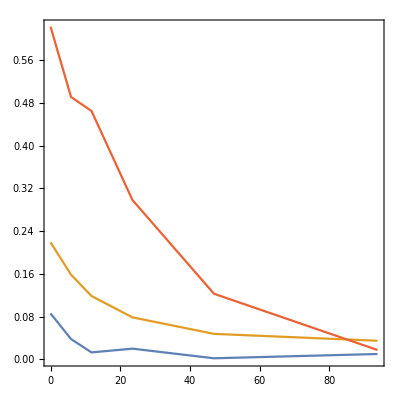

```mathematica
Needs["ErrorBarPlots`"];
points001err={{93.8,(1010-1000)/1000-(1010+0006-1000)/1000},
{46.9,(1002-1000)/1000-(1002+0007-1000)/1000},
{23.5,(1020-1000)/1000-(1020+0007-1000)/1000},
{11.75,(1013-1000)/1000-(1013+0002-1000)/1000},
{5.88,(1038-1000)/1000-(1038+0008-1000)/1000},
{0,(1086-1000)/1000-(1086+0006-1000)/1000}};
points001={{93.8,(1010-1000)/1000},
{46.9,(1002-1000)/1000},
{23.5,(1020-1000)/1000},
{11.75,(1013-1000)/1000},
{5.88,(1038-1000)/1000},
{0,(1086-1000)/1000}};
points001Plot=Table[{points001[[ii]],ErrorBar[-points001err[[ii,2]]]},{ii,1,Length[points001]}]
points01={{93.8,(8.03-7.76)/7.76},{46.9,(8.13-7.76)/7.76},{23.5,(8.37-7.76)/7.76},{11.75,(8.68-7.76)/7.76},{5.88,(8.99-7.76)/7.76},{0,(9.46-7.76)/7.76}};
points01err={{93.8,(8.03-7.76)/7.76-(8.03+0.04-7.76)/7.76},
{46.9,(8.13-7.76)/7.76-(8.13+0.03-7.76)/7.76},
{23.5,(8.37-7.76)/7.76-(8.37+0.07-7.76)/7.76},
{11.75,(8.68-7.76)/7.76-(8.68+0.09-7.76)/7.76},
{5.88,(8.99-7.76)/7.76-(8.99+0.09-7.76)/7.76},
{0,(9.46-7.76)/7.76-(9.46+0.04-7.76)/7.76}};
points01Plot=Table[{points01[[ii]],ErrorBar[-points01err[[ii,2]]]},{ii,1,Length[points01]}]

points01w={{93.8,(7.77-7.76)/7.76},{46.9,(7.85-7.76)/7.76},{23.5,(7.85-7.76)/7.76},{11.75,(8.31-7.76)/7.76},{5.88,(8.71-7.76)/7.76},{0,(8.98-7.76)/7.76}};
points01werr={{93.8,(7.77-7.76)/7.76-(7.77+0.02-7.76)/7.76},
{46.9,(7.85-7.76)/7.76-(7.85+0.03-7.76)/7.76},
{23.5,(7.85-7.76)/7.76-(7.85+0.02-7.76)/7.76},
{11.75,(8.31-7.76)/7.76-(8.31+0.02-7.76)/7.76},
{5.88,(8.71-7.76)/7.76-(8.71+0.02-7.76)/7.76},
{0,(8.98-7.76)/7.76-(8.98+0.02-7.76)/7.76}};
points01wPlot=Table[{points01w[[ii]],ErrorBar[-points01werr[[ii,2]]]},{ii,1,Length[points01w]}]

points01s={{93.8,(8.37-8.50)/8.50},{46.9,(8.41-8.50)/8.50},{23.5,(8.51-8.50)/8.50},{11.75,(8.70-8.50)/8.50},{5.88,(8.94-8.50)/8.50},{0,(9.43-8.50)/8.50}};
points01serr={{93.8,(8.37-8.50)/8.50-(8.37+0.02-8.50)/8.50},
{46.9,(8.41-8.50)/8.50-(8.41+0.03-8.50)/8.50},
{23.5,(8.51-8.50)/8.50-(8.51+0.02-8.50)/8.50},
{11.75,(8.51-8.50)/8.50-(8.51+0.02-8.50)/8.50},
{5.88,(8.70-8.50)/8.50-(8.70+0.02-8.50)/8.50},
{0,(8.94-8.50)/8.50-(8.94+0.02-8.50)/8.50}};
points01sPlot=Table[{points01s[[ii]],ErrorBar[-points01serr[[ii,2]]]},{ii,1,Length[points01s]}]


points05={{0,(4.7-3.34)/3.34},
{5.88,(4.4-3.34)/3.34},
{11.75,(4.21-3.34)/3.34},
{23.5,(3.95-3.34)/3.34},
{46.9,(3.63-3.34)/3.34},
{93.8,(3.54-3.34)/3.34}};
points05err={{0,(4.7-3.34)/3.34-(4.7+0.02-3.34)/3.34},{5.88,(4.4-3.34)/3.34-(4.4+0.2-3.34)/3.34},
{11.75,(4.21-3.34)/3.34-(4.21+0.03-3.34)/3.34},
{23.5,(3.95-3.34)/3.34-(3.95+0.02-3.34)/3.34},
{46.9,(3.63-3.34)/3.34-(3.63+0.02-3.34)/3.34},
{93.8,(3.54-3.34)/3.34-(3.54+0.05-3.34)/3.34}};
points05Plot=Table[{points05[[ii]],ErrorBar[-points05err[[ii,2]]]},{ii,1,Length[points05]}]

points20={{0,(1.85-1.14)/1.14},{5.88,(1.7-1.14)/1.14},{11.75,(1.67-1.14)/1.14},{23.5,(1.48-1.14)/1.14},{46.9,(1.28-1.14)/1.14},{93.8,(1.16-1.14)/1.14}};
points20err={{0,(1.85-1.14)/1.14-(1.85+0.02-1.14)/1.14},
{5.88,(1.7-1.14)/1.14-(1.7+0.1-1.14)/1.14},
{11.75,(1.67-1.14)/1.14-(1.67+0.03-1.14)/1.14},
{23.5,(1.48-1.14)/1.14-(1.48+0.03-1.14)/1.14},
{46.9,(1.28-1.14)/1.14-(1.28+0.02-1.14)/1.14},
{93.8,(1.16-1.14)/1.14}-(1.16+0.03-1.14)/1.14};
points20Plot=Table[{points20[[ii]],ErrorBar[-points20err[[ii,2]]]},{ii,1,Length[points20]}]
ListPlot[{points001,points01,points05Plot,points20},Joined->True,PlotRange->All,Axes->False,Frame->True,AspectRatio->1]
```

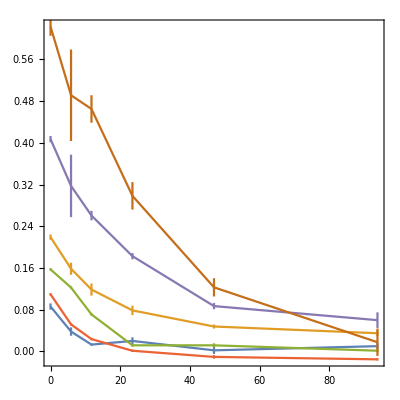

```mathematica
ErrorListPlot[{points001Plot,points01Plot,points01wPlot,points01sPlot,points05Plot,points20Plot},Joined->True,PlotRange->All,Axes->False,Frame->True,AspectRatio->1]
```

```mathematica
dims={13.06*10^-7,13.06*10^-7,6.53*10^-7};
domainParts=87;
wallPartsX = 40;
wallPartsZ = 20;
wallTotal = wallPartsX*wallPartsZ; 

xCell=dims[[1]]/wallPartsX;
zCell =dims[[3]]/wallPartsZ;

wallPosBottom = Flatten[Table[{xCell/2+xCell*ii,0.25*dims[[2]],xCell/2+zCell*jj},{ii,0,wallPartsX-1},{jj,0,wallPartsZ-1}],1];
wallPosTop = Flatten[Table[{xCell/2+xCell*ii,0.75dims[[2]],xCell/2+zCell*jj},{ii,0,wallPartsX-1},{jj,0,wallPartsZ-1}],1];
wallPos=Join[wallPosBottom,wallPosTop];

images=0;

wallPosPeriodic=Flatten[Table[Join[Flatten[Table[{xCell/2+xCell*ii+oo*dims[[1]],0.25*dims[[2]]+qq*dims[[2]],xCell/2+zCell*jj+pp*dims[[3]]},{ii,0,wallPartsX-1},{jj,0,wallPartsZ-1}],1],Flatten[Table[{xCell/2+xCell*ii+oo*dims[[1]],0.75*dims[[2]]+qq*dims[[2]],xCell/2+zCell*jj+pp*dims[[3]]},{ii,0,wallPartsX-1},{jj,0,wallPartsZ-1}],1]],{oo,-images,images},{pp,-images,images},{qq,-images,images}],2];
```

```mathematica
dims={16*104.48*10^-7,52.24*10^-7,52.24*10^-7};
count =(2*4096)/8
sep=dims[[1]]/count
images=0;
wallPos=Table[{sep/2+ii*sep,0.5dims[[2]],0.5dims[[3]]},{ii,0,count-1}];
(*wallPos={{0.5dims[[1]],0.5dims[[2]],0.5dims[[3]]},{0.375dims[[1]],0.5dims[[2]],0.5dims[[3]]},{0.625dims[[1]],0.5dims[[2]],0.5dims[[3]]}};*)
wallPosPeriodic=Table[{wallPos[[ii,1]],wallPos[[ii,2]],wallPos[[ii,3]]+qq*dims[[2]]},{qq,-images,images},{ii,1,Length[wallPos]}];
Length[wallPosPeriodic]
```

1024

1.6325×10^-7

1

```mathematica
dims={3.265*10^-7,52.24*10^-7,52.24*10^-7};
count =16/8
sep=dims[[1]]/count

wallPos=Table[{sep/2+ii*sep,0.5dims[[2]],0.5dims[[3]]},{ii,0,count-1}]
(*wallPos={{0.5dims[[1]],0.5dims[[2]],0.5dims[[3]]},{0.375dims[[1]],0.5dims[[2]],0.5dims[[3]]},{0.625dims[[1]],0.5dims[[2]],0.5dims[[3]]}};*)
wallPosPeriodic={wallPos};
```

2

1.6325×10^-7

{{8.1625×10^-8,2.612×10^-6,2.612×10^-6},{2.44875×10^-7,2.612×10^-6,2.612×10^-6}}

```mathematica
aa=2.561*10^-8;
μ=0.9*10^-2;
mob=Sum[ArrayFlatten[Table[Table[If[wallPos[[jj]]-wallPosPeriodic[[pp,ii]]=={0,0,0},dryTensor[{0,0,0},aa],RPY[wallPos[[jj]]-wallPosPeriodic[[pp,ii]],aa]],{ii,1,Length[wallPos]}],{jj,1,Length[wallPos]}]],{pp,1,Length[wallPosPeriodic]}];
(*mobGL=ArrayFlatten[Table[Table[RPY[wallPosBottom[[jj]]-wallPosBottomGL[[ii]],aa],{ii,1,Length[wallPosBottomGL]}],{jj,1,Length[wallPosBottom]}]];*)
```

```mathematica
Length[mob[[1]]]
Length[force]
count
```

192

192

64

```mathematica
mobInv=Inverse[matC];
```

```mathematica
q=1.6*10^-19;
f=10*10^12;
force=Flatten[Table[{q*f,0,0},{ii,1,count}]];
```

```mathematica
vel=mob.force;
vel[[2*256*3-2]]
vel[[2*256*3-2]]
```

1546.11

1546.11

```mathematica
g
```

```mathematica
dims={2*104.48*10^-7,52.24*10^-7,52.24*10^-7};
wallPos={{0.25*dims[[1]],0.5*dims[[2]],0.5*dims[[3]]},{0.75*dims[[1]],0.5*dims[[2]],0.5*dims[[3]]}}
```

{{3.265×10^-7,6.53×10^-7,3.265×10^-7},{9.795×10^-7,6.53×10^-7,3.265×10^-7}}

```mathematica
SetDirectory[NotebookDirectory[]];
file="/home/drladiges/gigan/projects/FHDeX/exec/immersedIons/matrixInv.dat";
BinaryWrite[file,Flatten[mobInv], "Real64"]
Close[file];
```

/home/drladiges/gigan/projects/FHDeX/exec/immersedIons/matrixInv.dat

```mathematica
posList=Table[{wallPos[[ii,1]],wallPos[[ii,2]],wallPos[[ii,3]],0},{ii,1,Length[wallPos]}];
SetDirectory[NotebookDirectory[]];
file="/home/drladiges/gigan/projects/FHDeX/exec/immersedIons/particles.dat";
Export[file,posList];
```

```mathematica
3.959505941910945e+02
```

```mathematica
dryTensor[{0,0,0},aa]
```

{{2.30169×10^8,0.,0.},{0.,2.30169×10^8,0.},{0.,0.,2.30169×10^8}}

```mathematica
SetDirectory[NotebookDirectory[]];
file="/home/drladiges/gigan/projects/FHDeX/exec/immersedIons/matOut";
matList=Flatten[Import[file,"Table"]];
```

```mathematica
sz=4800
mf[i_,j_]:=matList[[j+(i-1)sz]];
matC=Array[mf,{sz,sz}]
```

4800

{1}
 |  |  |  |

```mathematica
mobInv
```

{{6.13292×10^-8,6.74975×10^-12,8.911×10^-12,-1.85776×10^-8,6.69879×10^-12,-2.0644×10^-10,4.981×10^-9,6.79309×10^-12,2.09342×10^-10,4782,1.66443×10^-13,6.79327×10^-12,-1.78643×10^-14,2.85644×10^-13,6.6982×10^-12,1.97604×10^-14,2.38722×10^-13,6.75058×10^-12,-2.04898×10^-14},{1},4796,{1},{1}}
 |  |  |  |

```mathematica
matC[[1;;9,1;;9]]//MatrixForm
```

(2.29006×10^8 | 45.8832 | -9553.29 | 1.50508×10^8 | 44.9425 | 345785 | 7.40226×10^7 | 43.7493 | 143781
49.6517 | 2.06926×10^8 | 38.1314 | 49.4886 | 1.28124×10^8 | -161929 | 48.7247 | 5.14208×10^7 | -307772
-9553.37 | 36.7927 | 2.39393×10^8 | -348181 | 162082 | 1.94249×10^8 | -145366 | 307617 | 1.33088×10^8
1.50508×10^8 | 44.8455 | -348166 | 2.29628×10^8 | 45.9959 | 6647.93 | 1.49519×10^8 | 44.86 | 348191
49.4061 | 1.28124×10^8 | 162084 | 49.7318 | 2.0755×10^8 | -25.9049 | 49.3932 | 1.2713×10^8 | -162160
345784 | -161930 | 1.94249×10^8 | 6633.63 | -27.3817 | 2.38934×10^8 | -345091 | 161894 | 1.94698×10^8
7.40224×10^7 | 43.6773 | -145354 | 1.49519×10^8 | 44.8462 | -345079 | 2.28728×10^8 | 45.9546 | 0.170411
48.6783 | 5.14208×10^7 | 307619 | 49.3987 | 1.2713×10^8 | 161895 | 49.4642 | 2.06647×10^8 | 1.2745
143781 | -307773 | 1.33088×10^8 | 348178 | -162161 | 1.94698×10^8 | -11.6807 | 0.060827 | 2.39838×10^8)

```mathematica
matC[[-9;;-1,-9;;-1]]//MatrixForm
```

(2.28728×10^8 | 45.158 | -0.0975542 | 1.49519×10^8 | 44.0403 | -345080 | 7.40226×10^7 | 42.9873 | -145355
49.2244 | 2.06647×10^8 | 0.620287 | 49.2815 | 1.2713×10^8 | 161894 | 48.7956 | 5.14208×10^7 | 307618
-7.22873 | 0.0534654 | 2.39838×10^8 | 348178 | -162162 | 1.94698×10^8 | 143767 | -307774 | 1.33088×10^8
1.49519×10^8 | 44.0053 | 348191 | 2.29628×10^8 | 45.2157 | 6647.61 | 1.50508×10^8 | 44.0971 | -348166
48.9099 | 1.2713×10^8 | -162161 | 49.4748 | 2.0755×10^8 | -26.7924 | 49.4755 | 1.28124×10^8 | 162083
-345085 | 161894 | 1.94698×10^8 | 6635.5 | -27.3201 | 2.38934×10^8 | 345770 | -161930 | 1.94249×10^8
7.40226×10^7 | 42.9647 | 143781 | 1.50508×10^8 | 44.0585 | 345784 | 2.29006×10^8 | 45.1447 | -9553.57
48.2873 | 5.14208×10^7 | -307773 | 49.1729 | 1.28124×10^8 | -161930 | 49.6388 | 2.06926×10^8 | 37.3024
-145359 | 307618 | 1.33088×10^8 | -348177 | 162083 | 1.94249×10^8 | -9567.59 | 36.9019 | 2.39393×10^8)

```mathematica
nvel=1/(6 π μ aa);
wetData={{0.5,4.33862196*10^8/nvel},{1,3.89776*10^8/nvel},{2,2.84369221*10^8/nvel},{4,1.590170803003*10^8/nvel},{8,7.861751236889063*10^7/nvel}}
dampData={{0.5,2.188555567623945*10^8/nvel},{1,2.128614660916317*10^8/nvel},{2,1.9114440124419*10^8/nvel},{4,1.386998898093581*10^8/nvel},{8,7.6350224810953*10^7/nvel}}
```

{{0.5,0.950818},{1,0.854202},{2,0.623201},{4,0.348489},{8,0.172292}}

{{0.5,0.479627},{1,0.46649},{2,0.418897},{4,0.303964},{8,0.167323}}

```mathematica
m1=Graphics[{Thick,Red,Circle[{0,0},1]}];
m2=Graphics[{Thick,Red,Line[{{-0.5,-0.5},{0.5,-0.5},{0.5,0.5},{-0.5,0.5},{-0.5,-0.5}}]}];
m3=Graphics[{Thick,Black,Line[{{-0.5,-0.5},{0.5,0.5}}],Line[{{-0.5,0.5},{0.5,-0.5}}]}];
m4=Graphics[{Thick,Black,Line[{{0,-0.5},{-0.5,0},{0,0.5},{0.5,0},{0,-0.5}}]}];
ss=0.03;
```

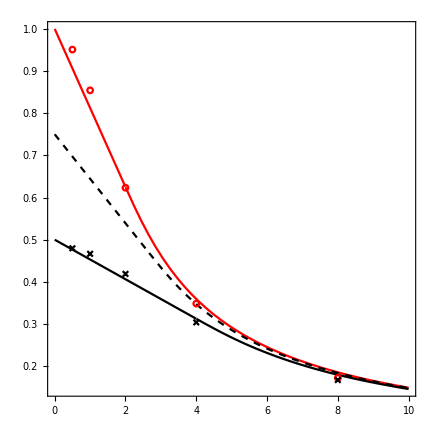

4.56304×10^8

```mathematica
aa=1.29182*10^-8;
paa=Plot[{(RPY[{x aa,0,0},aa].{1,0,0})[[1]](6 π μ aa),(RPY[{x aa,0,0},2aa].{1,0,0})[[1]](6 π μ aa),(RPY[{x aa,0,0},1.33333aa].{1,0,0})[[1]](6 π μ aa)},{x,0,10},PlotStyle->{Red,Black,{Black,Dashed}}];
pbb=ListPlot[{wetData,dampData},PlotMarkers->{{m1,ss},{m3,ss}},PlotStyle->{Red,Black}];
Show[paa,pbb,Axes->False,Frame->True,AspectRatio->1]
```

```mathematica
nvel=1/(6 π μ aa);
wetData={{0.5,4.16808522*10^8/nvel},{1,3.410819130*10^8/nvel},{2,1.87910207455024*10^8/nvel},{4,8.29870572051*10^7/nvel},{8,3.68865691791*10^7/nvel}}
dampData={{0.5,2.17998988*10^8/nvel},{1,2.0523165699549*10^8/nvel},{2,1.6736846128171*10^8/nvel},{4,9.078303775*10^7/nvel},{8,3.832321149528*10^7/nvel}}
```

{{0.5,0.913445},{1,0.747488},{2,0.411809},{4,0.181868},{8,0.0808377}}

{{0.5,0.477749},{1,0.449769},{2,0.366791},{4,0.198953},{8,0.0839861}}

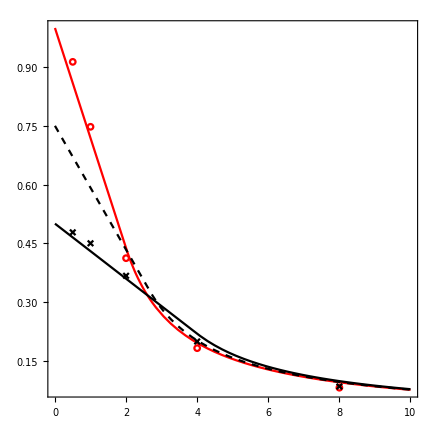

```mathematica
aa=1.29182*10^-8;
paa=Plot[{(RPY[{x aa,0,0},aa].{0,1,0})[[2]](6 π μ aa),(RPY[{x aa,0,0},2aa].{0,1,0})[[2]](6 π μ aa),(RPY[{x aa,0,0},1.33333aa].{0,1,0})[[2]](6 π μ aa)},{x,0,10},PlotStyle->{Red,Black,{Black,Dashed}}];
pbb=ListPlot[{wetData,dampData},PlotMarkers->{{m1,ss},{m3,ss}},PlotStyle->{Red,Black}];
Show[paa,pbb,Axes->False,Frame->True,AspectRatio->1]
```

```mathematica
paa=Plot[{(RPY[{x aa,0,0},aa].{1,0,0})[[1]](6 π μ aa),(RPY[{x aa,0,0},2aa].{1,0,0})[[1]](6 π μ aa),(RPY[{x aa,0,0},1.33333aa].{1,0,0})[[1]](6 π μ aa)},{x,0,10},PlotStyle->{Red,Black,{Black,Dashed}}];
pbb=ListPlot[{wetData,dampData},PlotMarkers->{{m1,ss},{m3,ss}},PlotStyle->{Red,Black}];
Show[paa,pbb,Axes->False,Frame->True,AspectRatio->1]
```

```mathematica
aa=1.62*10^-8;
RPY[{0 ,60*10^-8,0},aa].{1,0,0}
```

{6.63468×10^6,0.,0.}

```mathematica
1/(6 π μ aa)
```

3.27479×10^8